```mathematica
Manipulate[
Module[{f1,f2,f3,f4,f5},
f1=200;
f2=300;
f3[x_]:=-421*x^2-164*x+450;
f4[x_]:=-3929*x^2+6375*x-2211;
f5[x_]:=-2060*x^2+3334*x-973;

Show[Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->Black,Filling->#3,FillingStyle->Directive[#4,Opacity@0.6]]&@@@{
{f1,{0,0.8},Bottom,Hue@0},{f2,{0.8,1},Bottom,Hue@0.2},{f3[x],{0,0.6},f1,Hue@0.4},{f4[x],{0.6,0.8},f1,Hue@0.6},{f5[x],{0.8,1},f2,Hue@0.8}},
Graphics@{Line[{{0.8,100},{0.8,375}}],PointSize@0.03,Point[{comp,100+heat}]},
PlotRange->{{0,1},{100,500}},PlotRangePadding->None,Frame->True,FrameLabel->{Style["composition",17],Style["temeprature",17]},LabelStyle->{14,Black},ImageSize->400,AspectRatio->1]
],
Control[{{comp,0.3,"composition"},0,1,0.05,Appearance->"Labeled"}],
Control[{{heat,20,"add heat"},0,500,1,Appearance->"Labeled"}]
]
```

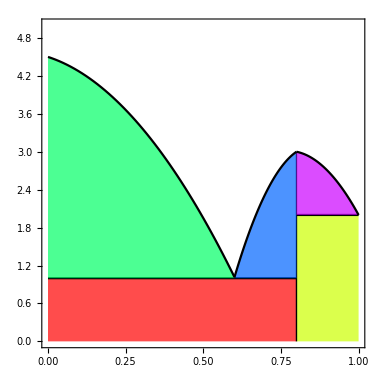

```mathematica
Module[{f1,f2,f3,f4,f5},
f1=1;
f2=2;
f3[x_]:=-7*x^2-1.6*x+4.5;
f4[x_]:=-33*x^2+56.15*x-20.8;
f5[x_]:=-20*x^2+31*x-9;

Show[Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->Black,Filling->#3,FillingStyle->Directive[#4,Opacity[0.7]]]&@@@{
{f1,{0,0.8},Bottom,Hue@0},{f2,{0.8,1},Bottom,Hue@0.2},{f3[x],{0,0.6},f1,Hue@0.4},{f4[x],{0.6,0.8},f1,Hue@0.6},{f5[x],{0.8,1},f2,Hue@0.8}},
Graphics@{Line[{{0.8,0},{0.8,3}}]},
PlotRange->{{0,1},{0,5}},PlotRangePadding->None,AxesOrigin->{0,0},Frame->True,LabelStyle->{14,Black},ImageSize->380,AspectRatio->1]
]
```